### Import “csv” file

```mathematica
bb00=Import["/Users/sinbi/Desktop/master/Plot_Dizitizer/1402.6703-bb,cc/bb-fullsky-100.csv","CSV","HearderLines"->1];
bb01=Table[{bb00[[i,1]],Log10[0.1*bb00[[i,2]]]},{i,7,Length[bb00]}];
bb02=Import["/Users/sinbi/Desktop/master/Plot_Dizitizer/1402.6703-bb,cc/bb-fullsky-80.csv","CSV","HearderLines"->1];
bb03=Table[{bb02[[i,1]],Log10[0.1*bb02[[i,2]]]},{i,7,Length[bb02]}];
bb04=Import["/Users/sinbi/Desktop/master/Plot_Dizitizer/1402.6703-bb,cc/bb-fullsky-50.csv","CSV","HearderLines"->1];
bb05=Table[{bb04[[i,1]],Log10[0.1*bb04[[i,2]]]},{i,7,Length[bb04]}];
```

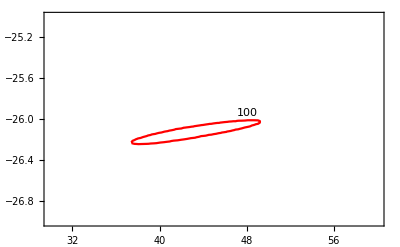

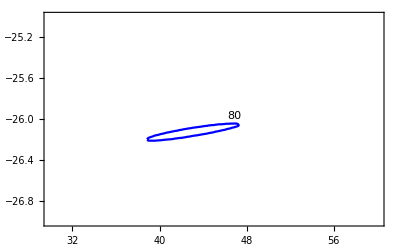

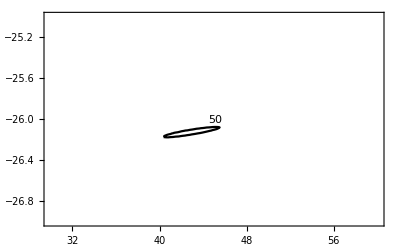

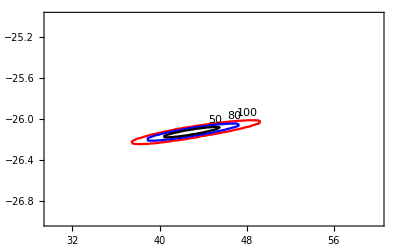

```mathematica
L1=ListLinePlot[bb01, PlotRange->{{30,60},{-27,-25}},PlotStyle->{Red},Frame->True,Axes->False,PlotLabels->Placed["100",Above]]
L2=ListLinePlot[bb03,PlotRange->{{30,60},{-27,-25}},PlotStyle->{Blue},Frame->True,Axes->False,PlotLabels->Placed["80",Above]]
L3=ListLinePlot[bb05, PlotRange->{{30,60},{-27,-25}},PlotStyle->{Black},Frame->True,Axes->False,PlotLabels->Placed["50",Above]]
L4=Show[L1,L2,L3]
```

### NFW,BUR,EIN

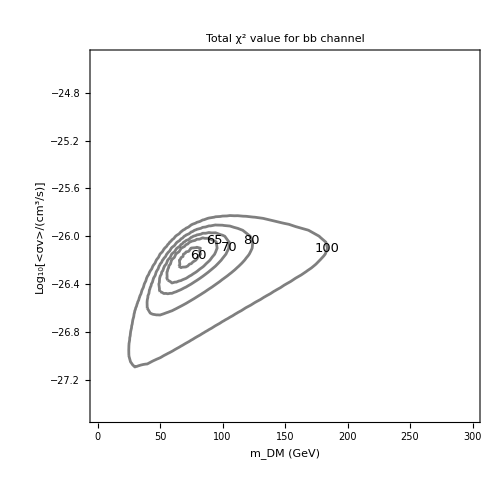

```mathematica
contlinebNFW=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/Total_particle/NFW/contour_AMS_bb_log.dat","Table",HeaderLines->1];
contbNFWLog=Table[{contlinebNFW[[i,1]],contlinebNFW[[i,2]], contlinebNFW[[i, 4]]},{i, Length[contlinebNFW]}];
PlotcontourBNFW=ListContourPlot[contbNFWLog,Contours-> {60,65,70,80,100},
FrameLabel->{Style["m_DM (GeV)",20,Black,Bold, FontFamily->Times], Style["Log_10[<σv>/(cm^3/s)]",20,Black,Bold, FontFamily->Times]},
FrameTicksStyle->Directive[Black, Bold, 16],
ContourLabels-> (Text[ Style[#3, Black, 13],{#1,#2}] &),ContourShading->None, ContourStyle ->{ {Black,Thickness[0.004]}},PlotLabel->Style["Total χ^2 value for bb channel",Black,20, Bold, FontFamily->"Times"],
ImageSize->500,PlotRange->{{0,300},{-27.5,-24.5}}
]
```

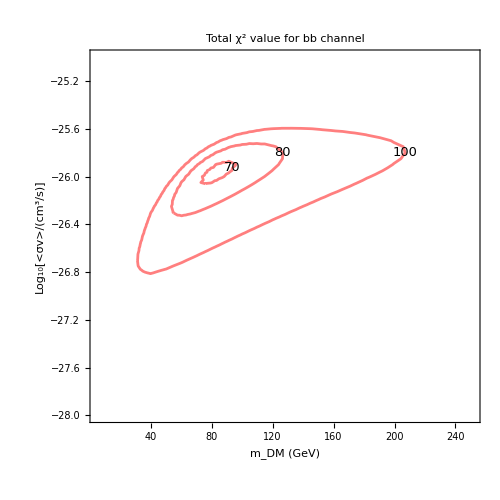

```mathematica
contlinebBur=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/Total_particle/Bur/contour_AMS_bb_log_Bur.dat","Table",HeaderLines->1];
contbBurLog=Table[{contlinebBur[[i,1]],contlinebBur[[i,2]], contlinebBur[[i, 4]]},{i, Length[contlinebBur]}];
PlotcontourBBur=ListContourPlot[contbBurLog,Contours-> {60,65,70,80,100},
FrameLabel->{Style["m_DM (GeV)",20,Black,Bold, FontFamily->Times], Style["Log_10[<σv>/(cm^3/s)]",20,Black,Bold, FontFamily->Times]},
FrameTicksStyle->Directive[Black, Bold, 16],
ContourLabels-> (Text[ Style[#3, Black, 13],{#1,#2}] &),ContourShading->None, ContourStyle ->{ {Red,Thickness[0.004]}},PlotLabel->Style["Total χ^2 value for bb channel",Black,20, Bold, FontFamily->"Times"],
ImageSize->500
]
```

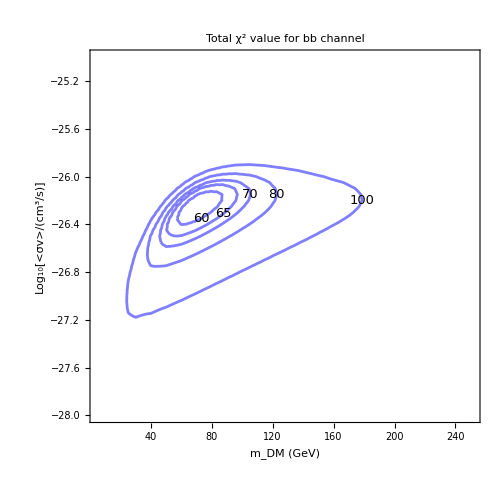

```mathematica
contlinebEin=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/Total_particle/Ein/contour_AMS_bb_log_Ein.dat","Table",HeaderLines->1];
contbEinLog=Table[{contlinebEin[[i,1]],contlinebEin[[i,2]], contlinebEin[[i, 4]]},{i, Length[contlinebEin]}];
PlotcontourBEin=ListContourPlot[contbEinLog,Contours-> {60,65,70,80,100},
FrameLabel->{Style["m_DM (GeV)",20,Black,Bold, FontFamily->Times], Style["Log_10[<σv>/(cm^3/s)]",20,Black,Bold, FontFamily->Times]},
FrameTicksStyle->Directive[Black, Bold, 16],
ContourLabels-> (Text[ Style[#3, Black, 13],{#1,#2}] &),ContourShading->None, ContourStyle ->{ {Blue,Thickness[0.004]}},PlotLabel->Style["Total χ^2 value for bb channel",Black,20, Bold, FontFamily->"Times"],
ImageSize->500
]
```

### MAX,MIN

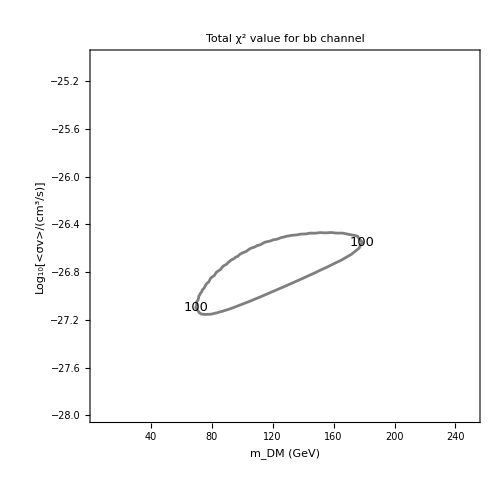

```mathematica
contlinebMAX=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/Total_particle/MAX/contour_AMS_bb_log_MAX.dat","Table",HeaderLines->1];
contbMAXLog=Table[{contlinebMAX[[i,1]],contlinebMAX[[i,2]], contlinebMAX[[i, 4]]},{i, Length[contlinebMAX]}];
PlotcontourBMAX=ListContourPlot[contbMAXLog,Contours-> {60,65,70,80,100},
FrameLabel->{Style["m_DM (GeV)",20,Black,Bold, FontFamily->Times], Style["Log_10[<σv>/(cm^3/s)]",20,Black,Bold, FontFamily->Times]},
FrameTicksStyle->Directive[Black, Bold, 16],
ContourLabels-> (Text[ Style[#3, Black, 13],{#1,#2}] &),ContourShading->None, ContourStyle ->{ {Black,Thickness[0.004]}},PlotLabel->Style["Total χ^2 value for bb channel",Black,20, Bold, FontFamily->"Times"],
ImageSize->500
]
```

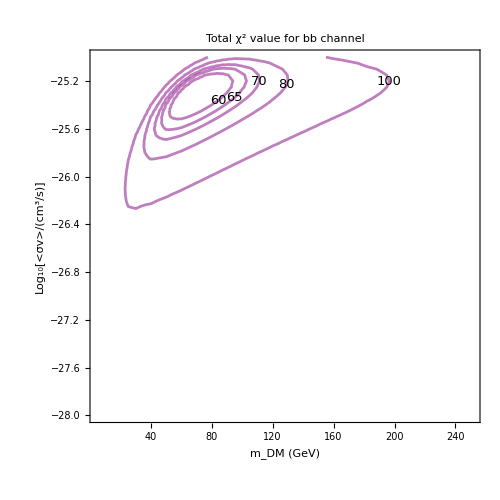

```mathematica
contlinebMIN=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/Total_particle/MIN/contour_AMS_bb_log_MIN.dat","Table",HeaderLines->1];
contbMINLog=Table[{contlinebMIN[[i,1]],contlinebMIN[[i,2]], contlinebMIN[[i, 4]]},{i, Length[contlinebMIN]}];
PlotcontourBMIN=ListContourPlot[contbMINLog,Contours-> {60,65,70,80,100},
FrameLabel->{Style["m_DM (GeV)",20,Black,Bold, FontFamily->Times], Style["Log_10[<σv>/(cm^3/s)]",20,Black,Bold, FontFamily->Times]},
FrameTicksStyle->Directive[Black, Bold, 16],
ContourLabels-> (Text[ Style[#3, Black, 13],{#1,#2}] &),ContourShading->None, ContourStyle ->{ {Purple,Thickness[0.004]}},PlotLabel->Style["Total χ^2 value for bb channel",Black,20, Bold, FontFamily->"Times"],
ImageSize->500
]
```

### Comparison

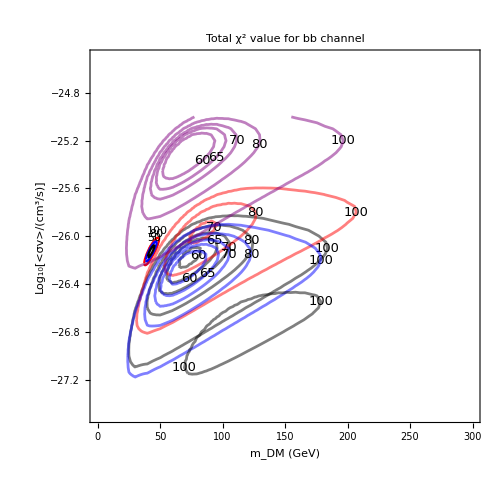

```mathematica
Show[PlotcontourBNFW,PlotcontourBBur,PlotcontourBEin,L4,PlotcontourBMAX,PlotcontourBMIN]
```

### 40*40 degree

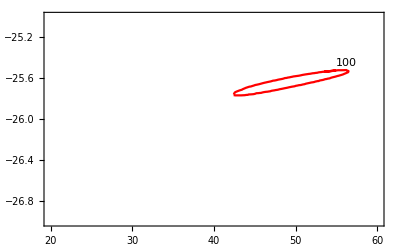

```mathematica
bb40=Import["/Users/sinbi/Desktop/bb-40-100.csv","CSV","HearderLines"->1];
bb401=Table[{bb40[[i,1]],Log10[0.1*bb40[[i,2]]]},{i,7,Length[bb40]}];
L401=ListLinePlot[bb401, PlotRange->{{20,60},{-27,-25}},PlotStyle->{Red},Frame->True,Axes->False,PlotLabels->Placed["100",Above]]
```

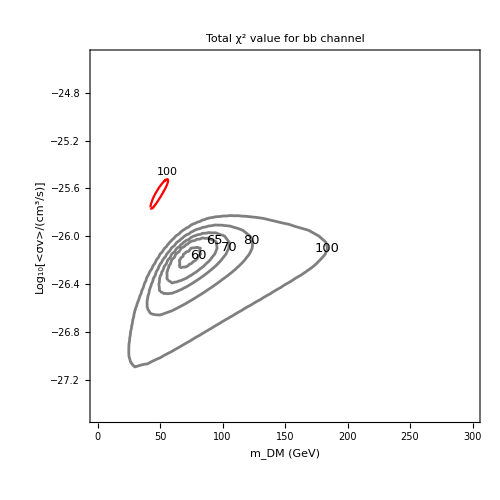

```mathematica
Show[PlotcontourBNFW,L401]
```

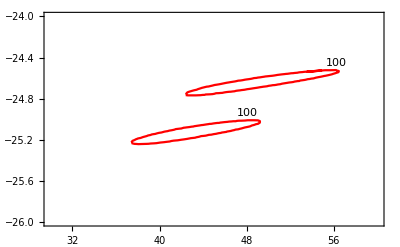

```mathematica
Show[L1,L401]
```